```mathematica
{Id,X,Y,Z}=Table[σ[i]=PauliMatrix[i],{i,0,3}];
```

```mathematica
TrS[W_]:=Module[{n=Length[W]/2},Tr[Partition[W,{n,n}],Plus,2]];
TrB[ρ_]:=Map[Tr,Partition[ρ,{2,2}],{2}];
ProjB[W_]:=KroneckerProduct[Id/2,TrS[W]];
ProjSB[W_]:=W-ProjB[W];
BathOps[W_]:=Module[{Id=IdentityMatrix[Length[W]/2]},Table[TrS[W.KroneckerProduct[σ[i],Id]]/2,{i,1,3}]]
FromBathOps[B_List]:=Sum[KroneckerProduct[σ[i],B⟦i⟧],{i,1,3}];
ErrorPhase[W_]:=Norm[ProjSB[W]]
TcpNorm[W_]:=Norm/@{ProjB[W],ProjSB[W]};
FcpNorm[W_]:=Norm/@BathOps[W];
```

```mathematica
RandomCSqMat[n_]:=RandomVariate[NormalDistribution[],{n,n}]+ⅈ RandomVariate[NormalDistribution[],{n,n}]
RandomHermitian[n_]:=Module[{A=RandomCSqMat[n]},A+A†]
RandomUnitary[n_]:=Module[{A=RandomCSqMat[n]},Orthogonalize[A]]
RandomBath0[n_:2]:=Module[{A=RandomHermitian[n]},Normalize[A-(Tr[A]/n) IdentityMatrix[n],Norm]]
RandomBathOps[n_:2]:=Module[{W=Sum[KroneckerProduct[σ[i],RandomHermitian[n]],{i,1,3}]},BathOps[Normalize[W,Norm]]]
RandomOmega[a_,b_,n_:2]:=a KroneckerProduct[σ[0],RandomBath0[n]]+b Normalize[Sum[KroneckerProduct[σ[i],RandomHermitian[n]],{i,1,3}],Norm]
RandomUniRot[θ_]:=Module[{ϕ=RandomReal[2π],z=RandomReal[{-1,1}],x,y,c,s},
{x,y}=√(1-z^2){Cos[ϕ],Sin[ϕ]};
{c,s}={Cos[θ],Sin[θ]};
{{ c- ⅈ z*s,(-ⅈ x-y)*s},{(-ⅈ x+y)*s,c+ⅈ z*s}}]
```

```mathematica
(* testing unitary invariance *)
Module[{Ω,U1,U2},
Ω=RandomOmega[0.1,0.2];
U1=KroneckerProduct[RandomUnitary[2],RandomUnitary[2]];
U2=RandomUnitary[4];
{TcpNorm[Ω],TcpNorm[U1.Ω.U1†],TcpNorm[U2.Ω.U2†]}
]
```

{{0.1,0.2},{0.1,0.2},{0.0740892,0.233371}}

```mathematica
Total/@%18
```

{0.3,0.3,0.30746}

```mathematica
PDD[U_]:=-KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U.KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U;
```

```mathematica
PDDMap[Ω_]:=Chop[ⅈ MatrixLog[PDD[MatrixExp[-ⅈ Ω]]]];
```

```mathematica
(* testing CDD *)
Module[{Ω,nconcat=5},
Ω=RandomOmega[0.01,0.02];
Transpose[{Range[0,nconcat],
ErrorPhase/@NestList[PDDMap,Ω,nconcat]}]
]
```

{{0,0.02},{1,0.000678255},{2,0.000171563},{3,0.000216247},{4,0.00278034},{5,0.00582822}}

```mathematica
ErrphUpper[n_,α_,β_]:=2^(n(n+1))α^n β*
Piecewise[{{2^n,β≤√(4^n-1)α},
{√(1+1/4((4^n-1)/(β/α)+β/α)^2),β>√(4^n-1)α}}]
```

```mathematica
ErrphUpper[0,a,b]
```

b (Piecewise[{{1, b≤0}, {√(1+b^2/(4 a^2)), b>0}, {0, True}}])

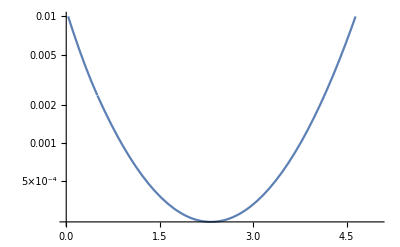

```mathematica
LogPlot[ErrphUpper[n,0.01,0.01],{n,0,5},PlotRange->{0,0.01}]
```

```mathematica
Module[{α=0.001,β=0.001,nconcat=8,Ω},
αn=Table[{n,4^n α},{n,0,nconcat}];
βn=Table[{n,2^(n^2+n)α^n β(2^n+1+β/α)},{n,0,nconcat}];
cddpts=
Table[Ω=RandomOmega[α,β];
Transpose[{Range[0,nconcat],ErrorPhase/@NestList[PDDMap,Ω,nconcat]}],{n,1,100}];
]
```

```mathematica
Needs["MaTeX`"]
```

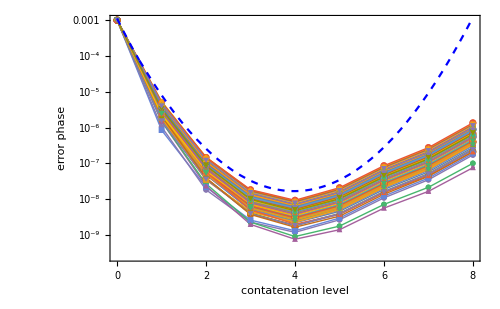

```mathematica
pic1=
Show[
ListLogPlot[cddpts,Mesh->Full,Joined->True,
PlotMarkers->{Automatic,Scaled[0.025]},
PlotStyle->Thin,
FrameTicks->{{Automatic,None},{Range[0,8],None}},
Frame->True,FrameLabel->{"contatenation level","error phase"},
ImageSize->500,FrameStyle->15
],
LogPlot[ErrphUpper[n,0.001,0.001],{n,0,8},PlotRange->All,
PlotStyle->Directive[Blue,Dashed]]
]
```

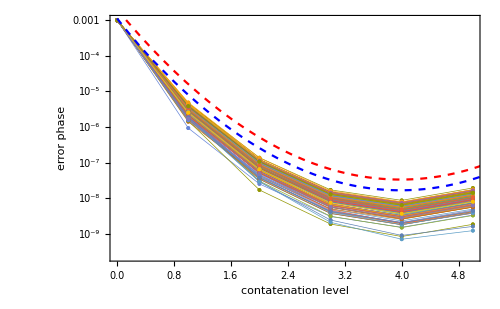

```mathematica
Module[{α=0.001,β=0.001,nconcat,cddpts},
nconcat=Ceiling[-Log[4,α]];
cddpts=
Table[
Transpose[{Range[0,nconcat],ErrorPhase/@NestList[PDDMap,RandomOmega[α,β],nconcat]}],{n,1,100}];
Show[ListLogPlot[cddpts,Joined->True,Mesh->Full,
PlotStyle->Thickness[0.001],
Frame->True,FrameLabel->{"contatenation level","error phase"},
ImageSize->500,FrameStyle->15,GridLines->Automatic
],
LogPlot[{ErrphUpper[n,α,β],
2^((n+1)^2)α^n β},{n,0,8},PlotRange->All,
PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed]}]
]]
```

```mathematica
Export[NotebookDirectory[]<>"../img/cdd-estimator.pdf",pic1]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/mathematica/../img/cdd-estimator.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/jiaan/Desktop/DD-threshold/dd-efficacy/mathematica/../img/cdd-estimator.pdf"]]]
```

```mathematica
Simplify[Maximize[4^1 α^2x1^2+(α x2 +β x1 x3)^2,{x1,x2,x3}∈Sphere[]][[1]],α>0&&β>0]
```

Piecewise[{{4 α^2, α≥Root[-β^4-6 β^2 #1^2+3 #1^4&,2]||√3 β≤3 α||α≤Root[-β^4-6 β^2 #1^2+3 #1^4&,1]}, {(9 α^4+10 α^2 β^2+β^4)/(4 β^2), √3 β>3 α}, {0, True}}]

```mathematica
Simplify[Maximize[4^2 α^2x1^2+(α x2 +β x1 x3)^2,{x1,x2,x3}∈Sphere[]][[1]],α>0&&β>0]
```

Piecewise[{{16 α^2, √15 β≤15 α}, {(225 α^4+34 α^2 β^2+β^4)/(4 β^2), √15 β>15 α}, {0, True}}]

```mathematica
Simplify[Maximize[4^3 α^2x1^2+(α x2 +β x1 x3)^2,{x1,x2,x3}∈Sphere[]][[1]],α>0&&β>0]
```

Piecewise[{{64 α^2, √7 β≤21 α}, {(3969 α^4+130 α^2 β^2+β^4)/(4 β^2), √7 β>21 α}, {0, True}}]

```mathematica
63^2
```

3969

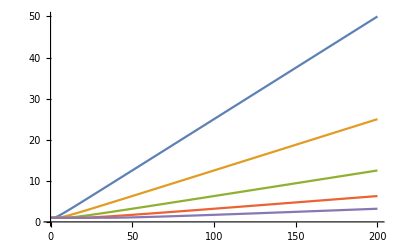

```mathematica
Plot[Evaluate[Table[
Piecewise[{{1,x≤√(4^n-1)},
{1/2^n √(1+1/4((4^n-1)/x+x)^2),x>√(4^n-1)}}]
,{n,1,5}]],{x,0,200}]
```

```mathematica
-Log[4,10^-3]-3/2
```

-3/2+Log[1000]/Log[4]

```mathematica
N[-3/2+Log[1000]/Log[4]]
```

3.48289

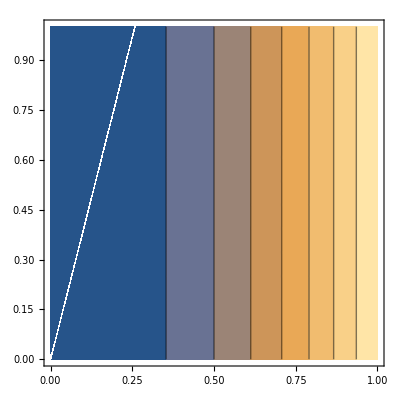

```mathematica
ContourPlot[Piecewise[{{16 α^2,√15 β≤15 α},{(225 α^4+34 α^2 β^2+β^4)/(4 β^2),√15 β>15 α}},0],{α,0,1},{β,0,1}]
```

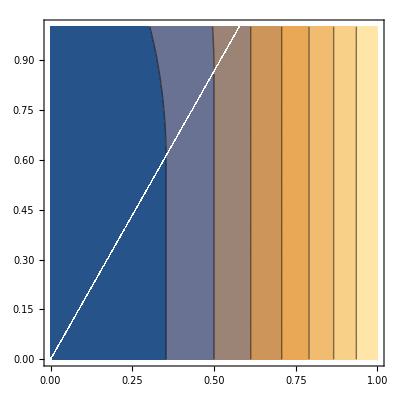

```mathematica
ContourPlot[Piecewise[{{4 α^2,α≥Root[-β^4-6 β^2 #1^2+3 #1^4&,2]||√3 β≤3 α||α≤Root[-β^4-6 β^2 #1^2+3 #1^4&,1]},{(9 α^4+10 α^2 β^2+β^4)/(4 β^2),√3 β>3 α}},0],{α,0,1},{β,0,1}]
```